```mathematica
PRÀCTICA 8:SÈRIES NUMÈRIQUES I SÈRIES DE POTÈNCIES
```

```mathematica
ACTIVITAT 1
```

```mathematica
Sum[2*k-1,{k,1,n}]
```

n^2

```mathematica
Per tant, la suma dels n primer nombres senars és:
∑_(k=1)^n (2k-1)=n^2
```

```mathematica
ACTIVITAT 2
```

```mathematica
Sum[(-1)^(n+1)/n^4,{n,1,Infinity}]
```

(7 π^4)/720

```mathematica
N[%,20]
```

0.94703282949724591758

```mathematica
Per tant, la suma de la sèrie és (7 π^4)/720, que es aproximadament igual a 0.947033
```

```mathematica
La suma parcial Subscript[s, 50] es:
```

```mathematica
Sum[(-1)^(n+1)/n^4,{n,1,50}]
```

17470536703024220936994645310482948982134539259776946224703621068376366744877866434243/18447658387025422739514525102807080738504090416169831450549480686220672755384320000000

```mathematica
N[%,20]
```

0.9470327526940530596

```mathematica
Comparant amb el valor aproximat de la suma de la sèrie, veiem que Subscript[s, 50] proporciona 6 decimals exactes.
```

```mathematica
ACTIVITAT 3
```

```mathematica
s[n_]=n/(2n+1)
```

n/(1+2 n)

```mathematica
Com Subscript[a, n]=Subscript[s, n]-Subscript[s, n-1], podem calcular fàcilment el terme general:
```

```mathematica
s[n]-s[n-1]
```

-(-1+n)/(1+2 (-1+n))+n/(1+2 n)

```mathematica
Simplify[%]
```

1/(-1+4 n^2)

```mathematica
Per tant, el terme general és Subscript[a, n]=1/(-1+4 n^2)
```

```mathematica
La suma de la sèrie és el limit de la successió de sumes parcials. Per tant, aquesta suma és:
```

```mathematica
Limit[s[n],n->Infinity]
```

1/2

```mathematica
ACTIVITAT 4
```

```mathematica
s[n_]=(-1)^(n+1)/(n*2^n)
```

((-1)^(1+n) 2^-n)/n

```mathematica
Sum[s[n],{n,1,Infinity}]
```

Log[3/2]

```mathematica
N[%]
```

0.405465

```mathematica
Per tant, la suma de la sèrie és Log[3/2], que és aproximadament igual a 0.405465.
```

```mathematica
ACTIVITAT 5
```

```mathematica
f[x_]=Log[(1+x)/(1-x)]
```

Log[(1+x)/(1-x)]

```mathematica
Series[f[x],{x,0,9}]
```

2 x+(2 x^3)/3+(2 x^5)/5+(2 x^7)/7+(2 x^9)/9+O[x]^10

```mathematica
Normal[%]
```

2 x+(2 x^3)/3+(2 x^5)/5+(2 x^7)/7+(2 x^9)/9

```mathematica
P[x_]=%
```

2 x+(2 x^3)/3+(2 x^5)/5+(2 x^7)/7+(2 x^9)/9

```mathematica
Per tant, el polinomi de McLaurin de grau 9 és: 2 x+(2 x^3)/3+(2 x^5)/5+(2 x^7)/7+(2 x^9)/9
```

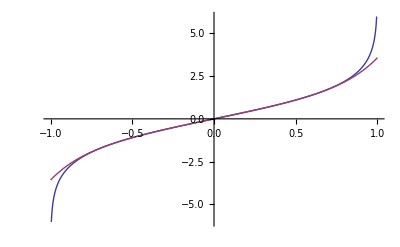

```mathematica
Plot[{f[x],P[x]},{x,-1,1}]
```

```mathematica
f[1/2]
```

Log[3]

```mathematica
Per tant, Log(3)=f(1/2).  Substuint en el polinomi de McLaurin x per 1/2:
```

```mathematica
P[1/2]
```

88583/80640

```mathematica
N[%,20]
```

1.0984995039682539683

```mathematica
L'aproximació obtinguda a partir del polinomi de McLaurin de grau 9 és 1.0984995039682539683.
```

```mathematica
Calculem ara el polinomi McLaurin de grau 20:
```

```mathematica
Series[f[x],{x,0,20}]
```

2 x+(2 x^3)/3+(2 x^5)/5+(2 x^7)/7+(2 x^9)/9+(2 x^11)/11+(2 x^13)/13+(2 x^15)/15+(2 x^17)/17+(2 x^19)/19+O[x]^21

```mathematica
Q[x_]=Normal[%]
```

2 x+(2 x^3)/3+(2 x^5)/5+(2 x^7)/7+(2 x^9)/9+(2 x^11)/11+(2 x^13)/13+(2 x^15)/15+(2 x^17)/17+(2 x^19)/19

```mathematica
Q[1/2]
```

4190187576017/3814073303040

```mathematica
N[%,20]
```

1.098612229785205969

```mathematica
L'aproximació obtinguda a partir del polinomi de McLaurin de grau 20 és 1.0986122297852059690.
```

```mathematica
N[Log[3],20]
```

1.0986122886681096914

```mathematica
Per tant, l'aproximació  a partir del polinomi de McLaurin de grau 20 garanteix 7 xifres decimals correctes.
```

```mathematica
ACTIVITAT 6
```

```mathematica
Calculem el polinomi de McLaurin de grau 8 de cos(x):
```

```mathematica
Series[Cos[x],{x,0,8}]
```

1-x^2/2+x^4/24-x^6/720+x^8/40320+O[x]^9

```mathematica
T[x_]=1-x^2/2+x^4/24-x^6/720+x^8/40320
```

1-x^2/2+x^4/24-x^6/720+x^8/40320

```mathematica
N[T[5/100],25]
```

0.9987502603949662465897817

```mathematica
L'aproximació de   cos(5/100) utilitzant el polinomi de MacLaurin de grau 8 és 0.99875026039496624658...(20 primers decimals)
```

```mathematica
Calculem una cota de l'error. Calcularem primer la derivada 9 de Cos[x]:
```

```mathematica
D[Cos[x],{x,9}]
```

-Sin[x]

```mathematica
Per tant, el valor absolut d'aquesta derivada està acotat per 1. Així, una  cota de l'error és:
```

```mathematica
1/9!*(5/100)^9
```

1/185794560000000000

```mathematica
N[%]
```

5.38229×10^-18

```mathematica
Així, l'error és menor que 10^(-17). L'aproximació te almenys 16 decimals exactes.
```

```mathematica
Comparem:
```

```mathematica
N[Cos[5/100],22]
```

0.9987502603949662465629

```mathematica
L'aproximació és: 0.9987502603949662465897817.
```

```mathematica
Veiem que, efectivament, tenen almenys 16 xifres decimals exactes.
```